```mathematica
Needs["NumericalCalculus`"]
```

```mathematica
SetDirectory[NotebookDirectory[]]
<<HQSimulation`
```

/home/ampolloreno/repos/qfi

Get::noopen: Cannot open PhysicsConstants`.

Needs::nocont: Context PhysicsConstants` was not created when Needs was evaluated.

```mathematica
SpinStates={2};
ModeCutoffs={};
GetOperators[SpinStates,ModeCutoffs,Display->True]
```

| Operator | Description
 | OpId | Identity operator
 | OpA | OpA[j] is the annihilation operator for mode j=1,2,3,...
 | OpAdag | OpAdag[j] is the creation operator for mode j=1,2,3,...
 | OpN | OpN[j] is the number operator for mode j=1,2,3,...
 | OpSwap | OpSwap[j,α=0,1,2,...,β=0,1,2,...] is the transition operator |β⟩⟨α| for ion j=1,2,3,...
 | Hilbert space dimension | HSdim=2

```mathematica
X=OpSwap[1,0,1]+OpSwap[1,1,0];
Y=ⅈ(OpSwap[1,0,1]-OpSwap[1,1,0]);
Z=-(OpSwap[1,1,1]-OpSwap[1,0,0]);
```

```mathematica
H[B_,ω_,t_]=π*X/2+B*Cos[ω t]Z;
vec0=Normalize[{1,1}]
```

{1/(√2),1/(√2)}

```mathematica
tmax=6;
b=1;
SEQSolve[H[1,1,t],vec0,{0,tmax}];
SEQSolve[H[0,1,t],vec0,{0,tmax},FinalState->True]
```

{-0.707107-1.23786×10^-7 ⅈ,-0.707107-1.23786×10^-7 ⅈ}

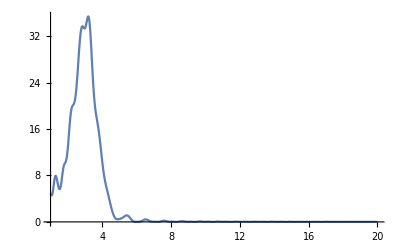

```mathematica
ψ[B_?NumericQ,ω_?NumericQ,T_?NumericQ]:= SEQSolve[H[B,ω,t],vec0,{0,T},FinalState->True];
ϕ[B_?NumericQ, ω_?NumericQ, T_?NumericQ] :=ND[ψ[ x, ω, T], x,B];
QFI[B_?NumericQ,ω_?NumericQ,T_?NumericQ]:=4 (Norm[ϕ[B,ω,T]]^2+ (Conjugate[ϕ[B,ω,T]].ψ[B,ω,T])^2);
Plot[Re[QFI[b, ω, tmax]], {ω,1,20}, PlotRange->All]
```

```mathematica
data=Cases[-Graphics-,Line[data_]:>data,-4,1][[1]];
Export["gX6.txt",data,"Table"]
```

gX6.txt

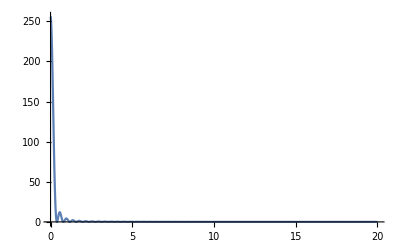

```mathematica
(*Ramsey*)
Plot[4 * ((Sin[ω*T] )/ω)^2/.T->tmax, {ω, 0, 20}, PlotRange->All]
```

```mathematica
data=Cases[-Graphics-,Line[data_]:>data,-4,1][[1]];
Export["ramsey.txt",data,"Table"]
```

ramsey.txt

```mathematica
$Assumptions={Element[{ω, B, T, b},Reals]};
XROT[θ_] := XROT[θ] = Cos[ θ/2]*PauliMatrix[4] - ⅈ*Sin[θ/2]*PauliMatrix[1];
Theta[t2_,t1_, ω_]:= Sin[ω*t2]/ω - Sin[ω*t1]/ω;
U[t2_, t1_, b_, ω_] := Cos[b*Theta[t2, t1, ω]]*PauliMatrix[4] - ⅈ*Sin[b*Theta[t2, t1, ω]]*PauliMatrix[3];
Dagger[X_] := Refine[Conjugate[Transpose[X]], {θ ∈ Reals, ω ∈ Reals}];
(* We'll assume everything is equally spaced, this is technically wlog since you can alwayas consider a longer sequence...*)
(* Produces the associated Z string unitary on the jth pulse*)
rhoT[n_, t_, θ_, b_?NumericQ, ω_] :=   Module[{},
rtn = PauliMatrix[4];
For[i=1,i<n + 1,i++,
rtn=XROT[ θ].U[t/n*(i), t/n*(i-1), b, ω].rtn//N;];
rtn]

InnProd[t_, k_, ω_?NumericQ]:=Module[{},
ϕ=1/Sqrt[2]*(ND[rhoT[t*2^k, t, π/(2^k), c, ω].{{1},{1}}, c, b])//N;
ψ = 1/Sqrt[2]*rhoT[t*2^k, t, π/(2^k), b, ω].{{1},{1}};
4*((ConjugateTranspose[ϕ].ϕ)[[1]][[1]] + ((ConjugateTranspose[ψ].ϕ)[[1]][[1]])^2)]
```

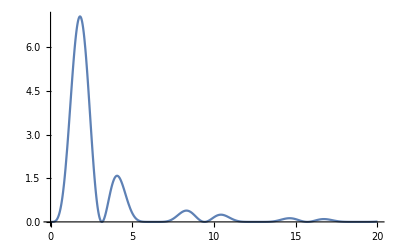

```mathematica
Plot[InnProd[tmax, 0, ω], {ω, 0, 20}, PlotRange->All]
```

```mathematica
data=Cases[-Graphics-,Line[data_]:>data,-4,1][[1]];
Export["pi.txt",data,"Table"]
```

pi.txt

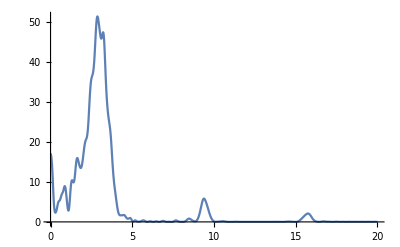

```mathematica
Plot[Re[InnProd[tmax, 1, ω]], {ω, 0, 20}, PlotRange->All]
```

```mathematica
data=Cases[-Graphics-,Line[data_]:>data,-4,1][[1]];
Export["pi2.txt",data,"Table"]
```

pi2.txt